## Classes 2

Лабораторная работа №2.  Символьные вычисления в системе Mathematica

#### I.1

Придумайте и определите символьное выражение, содержащее не менее трех слагаемых, причем хотя бы одно из них должно быть рациональным выражением

```mathematica
exp1=(4(x^2-y))/((3 x+2) (x^2+y^2))+x^3-y^2+y;
Expand[exp1](*раскрывает скобки*)
```

x^3+y-y^2+(4 x^2)/((2+3 x) (x^2+y^2))-(4 y)/((2+3 x) (x^2+y^2))

```mathematica
ExpandAll[exp1](*раскрывает все скобки*)
```

x^3+y-y^2+(4 x^2)/(2 x^2+3 x^3+2 y^2+3 x y^2)-(4 y)/(2 x^2+3 x^3+2 y^2+3 x y^2)

```mathematica
Factor[exp1](*выводит общие множители за скобки и представляет выражение в виде произведения множителей*)
```

1/((2+3 x) (x^2+y^2))(4 x^2+2 x^5+3 x^6-4 y+2 x^2 y+3 x^3 y-2 x^2 y^2-x^3 y^2+3 x^4 y^2+2 y^3+3 x y^3-2 y^4-3 x y^4)

```mathematica
Together[exp1](*складывает члены в сумму к общему знаменателю и отменяет множители в результате*)
```

(4 x^2+2 x^5+3 x^6-4 y+2 x^2 y+3 x^3 y-2 x^2 y^2-x^3 y^2+3 x^4 y^2+2 y^3+3 x y^3-2 y^4-3 x y^4)/((2+3 x) (x^2+y^2))

```mathematica
Apart[exp1](*переписывает рациональное выражение как сумму членов с минимальными знаменателями*)
```

x^3+y-y^2+(4 (x^2-y))/((2+3 x) (x^2+y^2))

```mathematica
Cancel[exp1]      (*убирает общие множители в числителе и знаменателе выражения*)
```

x^3+y-y^2+(4 (x^2-y))/((2+3 x) (x^2+y^2))

```mathematica
Simplify[exp1](*Возвращает простейшую форму выражения*)
```

x^3+y-y^2+(4 (x^2-y))/((2+3 x) (x^2+y^2))

#### I.2

Приведите выражение t1 к общему знаменателю и с помощью функции Numerator определите числитель полученного выражения, обозначив его t2. С помощью функции Collect представьте вырадение t2 в виде полинома по степеням x или y. Определите максимальную степень n одной из переменных, например, x в выражении t2 и коэффициент при x^n. Используйте функции Exponent и Coefficient

```mathematica
exp2=Numerator[Together[exp1]](*Возвращает числитель выражения exp1,приведенного к общему знаменателю*)
```

4 x^2+2 x^5+3 x^6-4 y+2 x^2 y+3 x^3 y-2 x^2 y^2-x^3 y^2+3 x^4 y^2+2 y^3+3 x y^3-2 y^4-3 x y^4

```mathematica
Collect[exp2,x](*объединяет члены по одинаковым степеням*)
```

2 x^5+3 x^6-4 y+3 x^4 y^2+2 y^3-2 y^4+x^2 (4+2 y-2 y^2)+x^3 (3 y-y^2)+x (3 y^3-3 y^4)

```mathematica
Exponent[exp2,x](*выводит максимальную степень х*)
```

6

```mathematica
Coefficient[exp2,x^2](*дает коэффициент формы в многочлене*)
```

4+2 y-2 y^2

#### 2

1. С помощью функции D вычислите производную функции x^n cos x.

```mathematica
D[x^n*Cos[x],x]
```

n x^(-1+n) Cos[x]-x^n Sin[x]

2. Вычислите следующие производные.

```mathematica
D[(1/x)*(a x^3+2 x^2),x] // Simplify
```

2+6 x

```mathematica
D[(1^3/x^3)(4 x^2-5x+8-3/x),x] // Simplify
```

(12-24 x+10 x^2-4 x^3)/x^5

```mathematica
D[(1^5/x^3 y^2)(x^3 y^2+3 x^2),x] // Simplify
```

-(3 y^2)/x^2

3. Используя функцию Integrate. Вычислите интеграл.

```mathematica
Integrate[1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

4. Вычислите интегралы, затем продифференцируйте полученные выражения и убедитесь в том, что получаемые результаты совпадают подынтегральными выражениями.

```mathematica
Integrate[x^3/(x^2+1),x]
```

x^2/2-1/2 Log[1+x^2]

```mathematica
Together[D[x^2/2-1/2 Log[1+x^2],x]]
```

x^3/(1+x^2)

```mathematica
Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
Simplify[Together[D[ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2],x]]]
```

1/(1+x^3)

5. Вычислите определенный интеграл.

```mathematica
∫_1^4 (5x-2 √x+32/x^3)ⅆx
```

259/6

6. Вычислите интегралы.

```mathematica
∫_0^1 (1+x^4)^(1/3)ⅆx
```

Hypergeometric2F1[-1/3,1/4,5/4,-1]

```mathematica
∫_0^1. (1+x^4)^(1/3)ⅆx
```

1.05753

```mathematica
1.0575277317789995
```

#### 3

1. Используя функцию Solve. решить уравнение.

```mathematica
Solve[a x^4+x^2+3==0,x]
```

{{x→-√(-1/6-(ⅈ √35)/6)},{x→√(-1/6-(ⅈ √35)/6)},{x→-√(-1/6+(ⅈ √35)/6)},{x→√(-1/6+(ⅈ √35)/6)}}

2. Найти точное решение системы уравнений.

```mathematica
Solve[x^2+y==1&&y^2-x^2==2,{x,y}] // Length
```

4

3. Решить систему уравнений.

```mathematica
NSolve[x^2-y^2==1&&y^3+x==5,{x,y}]
```

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

4. Найдите общие решения дифференциальных уравнений используя функцию DSolve. Самостоятельно задайте граничные условия и найдите соответстующие им частные решения. Постройте графики.

```mathematica
DSolve[{y'[x]-y[x]*Tan[x]==x,y[0]==0},y[x],x]
```

{{y[x]→1-Sec[x]+x Tan[x]}}

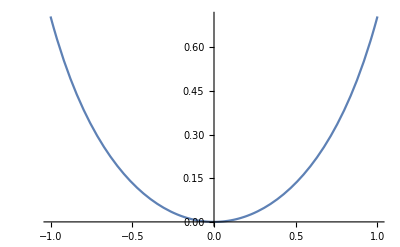

```mathematica
Plot[1-Sec[x]+x Tan[x],{x,-1,1}]
```

```mathematica
DSolve[{y'[x]+y[x]*Tan[x]==1/Cos[x],y[0]==0},y[x],x]
```

{{y[x]→Sin[x]}}

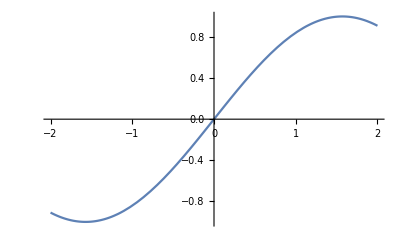

```mathematica
Plot[Sin[x],{x,-2,2}]
```

5. Самостоятельно выбрав граничные условия, найдите численное решение дифференциального уравнения в символьном виде.Затем с помощью NDSolve найдите численное решение этого уравнения. Интервал измерения x выберите самостоятельно.
На одной координатной плоскости постройте графики численного и символьного решений и покажите что они совпадают.

```mathematica
p1=DSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==1, y'[0]==1}, y[x], x] //FullSimplify
```

{{y[x]→1/2 ⅇ^(x/2) π (-(AiryAi[1/4]+2 AiryAiPrime[1/4]) AiryBi[1/4-x]+AiryAi[1/4-x] (AiryBi[1/4]+2 AiryBiPrime[1/4]))}}

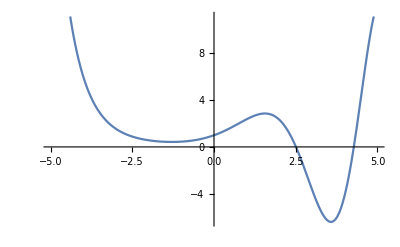

```mathematica
Plot[1/2 ⅇ^(x/2) π (-(AiryAi[1/4]+2 AiryAiPrime[1/4]) AiryBi[1/4-x]+AiryAi[1/4-x] (AiryBi[1/4]+2 AiryBiPrime[1/4])),{x,-5,5}]
```

```mathematica
NDSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==1, y'[0]==1}, y[x], {x, -7,7}]
```

{{y[x]→InterpolatingFunction[…][x]}}

```mathematica
Plot[InterpolatingFunction[…][x],{x,-5,5}]
```

-Graphics-